```mathematica
Clear[f,g,h,k,x]
```

```mathematica
(*Farey function*)
```

```mathematica
f[x_]=If[x>0&&x<=1/2,(x/(1-x)),((1-x)/x)]
```

If[x>0&&x≤1/2,x/(1-x),(1-x)/x]

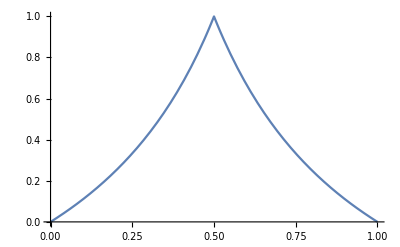

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
(*Hyper-Farey function*)
```

```mathematica
g[x_]=f[f[f[x]]]
```

If[If[If[x>0&&x≤1/2,x/(1-x),(1-x)/x]>0&&If[x>0&&x≤1/2,x/(1-x),(1-x)/x]≤1/2,If[x>0&&x≤1/2,x/(1-x),(1-x)/x]/(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x]),(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x])/If[x>0&&x≤1/2,x/(1-x),(1-x)/x]]>0&&If[If[x>0&&x≤1/2,x/(1-x),(1-x)/x]>0&&If[x>0&&x≤1/2,x/(1-x),(1-x)/x]≤1/2,If[x>0&&x≤1/2,x/(1-x),(1-x)/x]/(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x]),(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x])/If[x>0&&x≤1/2,x/(1-x),(1-x)/x]]≤1/2,If[If[x>0&&x≤1/2,x/(1-x),(1-x)/x]>0&&If[x>0&&x≤1/2,x/(1-x),(1-x)/x]≤1/2,If[x>0&&x≤1/2,x/(1-x),(1-x)/x]/(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x]),(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x])/If[x>0&&x≤1/2,x/(1-x),(1-x)/x]]/(1-If[If[x>0&&x≤1/2,x/(1-x),(1-x)/x]>0&&If[x>0&&x≤1/2,x/(1-x),(1-x)/x]≤1/2,If[x>0&&x≤1/2,x/(1-x),(1-x)/x]/(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x]),(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x])/If[x>0&&x≤1/2,x/(1-x),(1-x)/x]]),(1-If[If[x>0&&x≤1/2,x/(1-x),(1-x)/x]>0&&If[x>0&&x≤1/2,x/(1-x),(1-x)/x]≤1/2,If[x>0&&x≤1/2,x/(1-x),(1-x)/x]/(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x]),(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x])/If[x>0&&x≤1/2,x/(1-x),(1-x)/x]])/If[If[x>0&&x≤1/2,x/(1-x),(1-x)/x]>0&&If[x>0&&x≤1/2,x/(1-x),(1-x)/x]≤1/2,If[x>0&&x≤1/2,x/(1-x),(1-x)/x]/(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x]),(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x])/If[x>0&&x≤1/2,x/(1-x),(1-x)/x]]]

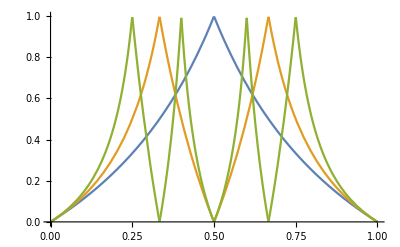

```mathematica
Plot[{f[x],f[f[x]],f[f[f[x]]]},{x,0,1}]
```

```mathematica
ff[x_]=g[Mod[Abs[x],1]]
```

If[If[If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]>0&&If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]≤1/2,If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]/(1-If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]),(1-If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]])/If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]]>0&&If[If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]>0&&If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]≤1/2,If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]/(1-If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]),(1-If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]])/If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]]≤1/2,If[If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]>0&&If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]≤1/2,If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]/(1-If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]),(1-If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]])/If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]]/(1-If[If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]>0&&If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]≤1/2,If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]/(1-If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]),(1-If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]])/If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]]),(1-If[If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]>0&&If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]≤1/2,If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]/(1-If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]),(1-If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]])/If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]])/If[If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]>0&&If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]≤1/2,If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]/(1-If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]),(1-If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]])/If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]/(1-Mod[Abs[x],1]),(1-Mod[Abs[x],1])/Mod[Abs[x],1]]]]

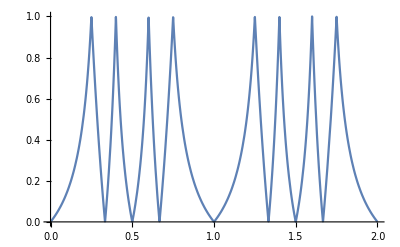

```mathematica
Plot[g[Mod[Abs[x],1]],{x,0,2}]
```

```mathematica
s0=Log[2]/Log[3]
```

Log[2]/Log[3]

```mathematica
hh[x_]=Sum[ff[2^k*x]/2^(s0*k),{k,0,20}];
```

```mathematica
kk[x_]=Sum[ff[2^k*(x+1/4)]/2^(s0*k),{k,0,20}];
```

```mathematica
ll[x_]=Sum[ff[2^k*(x-1/4)]/2^(s0*k),{k,0,20}];
```

```mathematica
g0=ParametricPlot[{hh[t],kk[t]},{t,0,1},PlotPoints->200,Axes->False,ColorFunction->Hue,ImageSize->2000];
```

```mathematica
g1=ParametricPlot3D[{hh[t],kk[t],ll[t]},{t,0,1},PlotPoints->200,Axes->False,ColorFunction->Hue,ImageSize->2000,ViewPoint->{2,2,2}];
```

```mathematica
Export["biscuit_Hyper_Farey2nd_quarterPhase_scale3_color.jpg",GraphicsGrid[{{g0,g1}},ImageSize->{4000,2000}]]
```

```mathematica
(*end*)
```